Precompression: u_0=0.3

```mathematica
SetDirectory[NotebookDirectory[]];
mat = Import["Displacementspoint3.txt","Table"];
plots=Table[ListPlot[-mat[[All,10i]],Joined->True,PlotRange-> {-0.2,2.6},Frame->True,PlotLegends->Placed[{"Precompresion = 0.3"},{Right,Bottom}],FrameLabel->{"POSITION OF NODES (x)","DISPLACEMENT (u(x,t))"}],{i,1,80}];
ListAnimate[plots]
```

```mathematica
Export["precompression.avi",plots]
```

precompression.avi

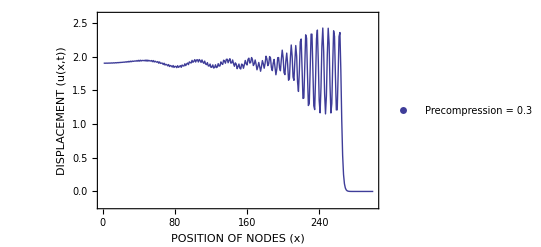

```mathematica
ListPlot[-mat[[All,840]],Joined->True,PlotRange-> {-0.2,2.6},Frame->True,PlotLegends->Placed[{"Precompression = 0.3"},{Left,Bottom}],FrameLabel->{"POSITION OF NODES (x)","DISPLACEMENT (u(x,t))"}]
```

Precompression: u_0=0.1

```mathematica
SetDirectory[NotebookDirectory[]];
mat = Import["Displacementspoint1.txt","Table"];
plots=Table[ListPlot[-mat[[All,2i]],Joined->True,PlotRange-> {-2.2,2.6},Frame->True,FrameLabel->{"POSITION OF NODES (x)","DISPLACEMENT (u(x,t))"},PlotLegends->Placed[{"Precompresion = 0.1"},{Right,Bottom}]],{i,1,749}];
ListAnimate[plots]
```

Dispersive Shock Waves